## *** Viz Preliminaries [old]

```mathematica
Clear@getShowable;getShowable[str_,showables_]:=ListQ@FirstPosition[showables,str];(* when not found returns "Missing[]"*)
```

```mathematica
Clear@drTriData;
Options@drTriData={sameClr->False};
drTriData[a_,triData_,triStr_,clr_,showables_,OptionsPattern[]]:=Module[{tri,npc,inc,tps,npcClr,incClr,lgt=.33},
tri=triData["tri"];
npc=triData["npc"];
inc=triData["inc"];
tps=triData["tps"];
npcClr=If[OptionValue@sameClr,clr,"npc"/.ptClrs];
incClr=If[OptionValue@sameClr,clr,"inc"/.ptClrs];
{FaceForm@None,PointSize@Large,
If[getShowable[triStr,showables],
{clr,
EdgeForm@{Thick,clr},Polygon@tri,Point@tri},{}],
If[getShowable[triStr<>"npc",showables],
{npcClr,
{Point@npc,drawOneNotable[npcClr,npc,OverBar["9"],0,-1.5,16]},
{Thick,Circle[npc,triData["npcR"]]}}
,{}],
If[getShowable[triStr<> "incirc",showables],
{incClr,
{Point@inc,drawOneNotable[incClr,inc,OverBar["I"],0,-1.5,16],Point@tps},
{Dashed,Line[{inc,#}]&/@tps},
{Thick,Circle[inc,triData["incR"]]}},{}],
If[getShowable[triStr<>"contact",showables],Module[{ns},
ns=norm/@(ellGrad[a,Sequence@@#]&/@tps);
{incClr,EdgeForm@{incClr,Dashed},Point@tps,Polygon@tps,
MapThread[Text[Style[#1,16],#2-.5*lgt*#3]&,{{"C_1","C_2","C_3"},tps,ns}]}],{}]}];
```

```mathematica
Clear@subscrCtr;subscrCtr[str_]:=Module[{ds},
ds=StringCases[str,DigitCharacter..][[1]];
Subscript["X",ds]]
```

```mathematica
drawNewCenters[orbit_,sides_]:=Module[{ctrs},
ctrs=getNewCenters[orbit,sides];
Graphics[{PointSize@Medium,Red,Point[Third/@ctrs],Text[subscrCtr[#[[1]]],#[[3]],{0,-1.5}]&/@ctrs}]];
```

```mathematica
Clear@drawSimT;
(* precompute loci *)
Options@drawSimT={ImageSize->800,labExtra->"",showablesOpt->{}};
drawSimT[a_,t_,ellPlot_,causticPlot_,loci_,opt:OptionsPattern[]]:=Module[{showables,incPlot,ellP,orbitData,orbit,normals,notables,exc,npc,
excNormals,excNotables,excCircleData,excOrtFeet,medians,excTps,orthic,
sides,pl,actData,medData,
x40,x88,x144 (*darboux*),x168,
x142,mosesPts,mosesOpts,hasMoses,
toShowNeedsGr,toShowGr,lgt=.33},
showables=OptionValue@showablesOpt;
ellP=N@{a Cos@t,Sin@t};
orbitData=getOrbitData[a,ellP[[1]],posY->(ellP[[2]]>0)];
orbit="orbit"/.orbitData;
sides=RotateLeft@triLengths@orbit;
normals="normals"/.orbitData;
notables=getNotables[orbit,normals];
exc="exc"/.notables;
medians="medians"/.notables;
npc="npc" /.notables;
excNormals=getTriBisectors@@exc;
excNotables=getNotables[exc,excNormals];
excOrtFeet=getAltBases@@exc;
excCircleData=getExcircleData[orbit,exc(*12,23,31*),npc];
excTps="tps"/.excCircleData;
orthic=getOrthicData@orbit;
actData=getAnticomplData[orbit,sides];
medData=getMedialData[orbit,sides];
(* bar + (bar-mitten)/2 = (3 bar - mitten)/2 *)
x142=(3("bar"/.notables)-("mitten"/.excCircleData))/2;
x144=getX144Trilin[orbit,sides];
x40=getBevanTrilin[orbit,sides];
x88=getX88Trilin[orbit,sides];
x168=getX168Trilin[orbit,sides];
mosesOpts=getShowable[#,showables]&/@{"mosesptsto1k","mosesptsto4k","mosesptsabove4k"};
hasMoses=Or@@mosesOpts;
mosesPts=If[hasMoses,getMosesTrilinears[orbit,sides],{}];
pl=OptionValue@labExtra<>"a="<>nf@a<>"; t="<>nf0@toDeg[t]<>"°";
toShowGr={ellPlot,
If[getShowable["orbit",showables],drawOrbit[orbitData,2*lgt,getShowable["normals",showables]],{}],
If[getShowable["caustic",showables],causticPlot,{}],
If[getShowable["loci",showables],loci,{}],
If[getShowable["notablelines",showables],drawNotableLines@notables,{}],(* remove excenters from here *)
If[getShowable["basicnotables",showables],drawBasicNotables@notables,{}],(* remove excenters from here *)
If[getShowable["notables",showables],drawNotables@notables,{}],(* remove excenters from here *)
If[getShowable["exnotablelines",showables],drawNotableLines@excNotables,{}],
If[getShowable["exnotables",showables],drawNotables[excNotables,"x"],{}],
If[getShowable["anticomplcircumb",showables],drawCircumMit[actData["tri"],ctrLab->"X_7",ps->("anticompl"/.ptClrs)],{}],
If[getShowable["medialcircumb",showables],drawCircumMit[medData["tri"],ctrLab->"X_142",ps->("med"/.ptClrs)],{}],
If[getShowable["excentralcircumb",showables],drawCircumMit[exc,ctrLab->"X_168",ps->("dar"/.ptClrs)],{}],
If[getShowable["steinercircumell",showables],drawCircumBar[orbit,ctrLab->"X_2",ps->{Dashed,("steiner"/.ptClrs)}],{}],
If[getShowable["inccircumell",showables],drawCircumInc[orbit,ctrLab->"X_1",ps->{Dashed,("inc"/.ptClrs)}],{}],
If[getShowable["hypx100",showables],showHyp5vizapp[a,toDeg@t,getHypX100,(Symbol@"lgt")->.1,ps->Darker@("inc"/.ptClrs)],{}],
If[getShowable["hypfeuerbach",showables],showHyp5vizapp[a,toDeg@t,getHypFeuerbach,(Symbol@"lgt")->.1,ps->("feu"/.ptClrs)],{}],
If[getShowable["trilinpts",showables],drawNewCenters[orbit,sides],{}]
};
toShowNeedsGr={
(* circles *)
If[getShowable["incircle",showables],{"inc"/.ptClrs,PointSize@Large,Point["inc"/.notables],
{Thick,Circle["inc"/.notables,"incRadius"/.notables]},
drawOneNotable["inc"/.ptClrs,"inc"/.notables,"I",0,-1.5,16]},{}],
If[getShowable["circumcircle",showables],{"cir"/.ptClrs,PointSize@Large,Point["cir"/.notables],
{Thick,Circle["cir"/.notables,"cirRadius"/.notables]},
drawOneNotable["cir"/.ptClrs,"cir"/.notables,"C",0,-1.5,16]},{}],
If[getShowable["excircles" ,showables],{"exc"/.ptClrs,
{PointSize@Large,Point@exc},
{Thick,MapThread[Circle[#1,#2]&,{exc,"radii" /.excCircleData}]}
},{}],
If[getShowable["ninepointcircle",showables],{"npc"/.ptClrs,PointSize@Large,Point["npc"/.notables],
{Thick,Circle["npc"/.notables,"npcRadius"/.notables]},
drawOneNotable["npc"/.ptClrs,"npc"/.notables,"9",0,-1.5,16]},{}],

(* lines *)
If[getShowable["interfeuerline",showables],{Dashed,Gray,Line[{"antifeu","feu"}/.notables]},{}],
If[getShowable["feuerbachline",showables],{Black,Dashed,Line[{"feu"/.notables,"npc"/.notables}]},{}],
If[getShowable["darbouxgergonneline",showables],
{"bar"/.ptClrs,Thick,Line[{"ger"/.notables,x144}]},{}],
If[getShowable["mittengergonneline",showables],
{"bar"/.ptClrs,Thick,Line[{"ger"/.notables,"mit"/.notables}]},{}],
If[getShowable["mittenx142line",showables],
{"bar"/.ptClrs,Thick,Line[{"mit"/.notables,x142}]},{}],
If[getShowable["x88antifeuerline",showables],{Dashed,Darker@Cyan,Line[{"antifeu","x88"}/.notables]},{}],
If[getShowable["inc2nagel",showables],{"nag"/.ptClrs,Line[{"nagel"/.excCircleData,"inc"/.notables}]},{}],
If[getShowable["darbouxlines",showables],
{Dashed,PointSize@Large,Red,
(*MapThread[Line@{#1,ray[#1,#2-#1,5]}&,{actData["tri"],RotateLeft@excTps}],*)
MapThread[Line[{#1,#2}]&,{actData["tri"],actData["tps"]}]
(*,Point@dbx,Cyan,Point@getX144Trilin[orbit,sides]*)},{}],
If[getShowable["antiorthicaxis",showables],drawAntiOrthicAxis[orbit,RotateLeft@exc,False],{}],
If[getShowable["isotomicaxis",showables],drawIsotomicAxis[orbit,sides,actData,Darker@Cyan],{}],

(* exc objects *)
If[getShowable["exbisectors",showables],{("exc"/.ptClrs),FaceForm[None],Arrowheads[Medium],MapThread[Arrow[{#1,ray[#1,#2,.5]}]&,{exc,excNormals}]},{}],
If[getShowable["exfeuerbach" ,showables],
{PointSize@Medium,("npc"/.ptClrs),Point["feus"/.excCircleData]},{}],
If[getShowable["exbaricenter",showables],{PointSize@Large,drawOneNotable["bar"/.ptClrs,"bar"/.excNotables,"xB"]
},{}],
If[getShowable["exnpc",showables],{("npc"/.ptClrs),Thick,Circle[npc,"npcRadius"/.excNotables]},{}],

(* triangles *)
drTriData[a,actData,"anticompl","anticompl"/.ptClrs,showables,sameClr->True],
drTriData[a,medData,"medial","med"/.ptClrs,showables,sameClr->True],
If[getShowable["extouchtri" ,showables],{FaceForm@None,EdgeForm@{Thick,"exc"/.ptClrs},Polygon@excTps},{}],
If[getShowable["excentral",showables],{FaceForm[None],EdgeForm[{Thick,("exc"/.ptClrs)}],Polygon@exc,("exc"/.ptClrs),PointSize@Large,Point@exc},{}],
If[getShowable["hexyltriangle",showables],Module[{hex},
hex=hexylTriangle[orbit,sides];
{FaceForm@None,EdgeForm["hex"/.ptClrs],Polygon@hex,PointSize@Medium,"hex"/.ptClrs,Point@hex}],{}],
If[getShowable["outernapoleon",showables],Module[{nap},
nap=outerNapoleonTriangle[orbit,sides];
{FaceForm@None,EdgeForm["nap"/.ptClrs],Polygon@nap,PointSize@Medium,"nap"/.ptClrs,Point@nap}],{}],
If[getShowable["morleytriangle",showables],Module[{morley,c1},
morley=firstMorleyTriangle[orbit,sides];
c1=getFirstMorleyTrilin[orbit,sides];
{FaceForm@None,EdgeForm["nap"/.ptClrs],Polygon@morley,PointSize@Medium,"nap"/.ptClrs,Point@morley,Black,Point@c1}],{}],
If[getShowable["orthictriangle",showables],{
{EdgeForm@Black,FaceForm[{"ort"/.ptClrs,Opacity@.3}],Polygon["feet"/.orthic]},
{EdgeForm["inc"/.ptClrs],FaceForm[{Lighter@Green,Opacity@.3}],Polygon["intouch"/.orthic],Gray,Circle["inc"/.orthic,"inradius"/.orthic]},
{FaceForm@None,EdgeForm@Red,Polygon["intouchOrt"/.orthic],Red,Point["intouchOrtInc"/.orthic]},
{PointSize@Medium,"ort"/.ptClrs,Point["feet"/.orthic],PointSize@Large,Point["ort"/.notables](*,drawOneNotable["ort"/.ptClrs,"ort"/.notables,"O"]*)},
(*{Dashed,Gray,MapThread[Line[{#1,#2}]&,{orbit,ortFeet}]},*)
{Dashed,Gray,Line[{#,"ort"/.notables}]&/@orbit},
{PointSize@Large,"inc"/.ptClrs,Point["inc"/.orthic]}},{}],
If[getShowable["experimental",showables],Module[{cir="cir"/.notables,rad,equi,xfeus,xfeusCir,xtpsCir,cirClr,medsCir},
cirClr="cir"/.ptClrs;
rad="cirRadius"/.notables;
xfeus=("feus"/.excCircleData);
equi=(cir+#)&/@(rad getEquilateral[0.]);
xfeusCir=getCircumcenter@@xfeus;
xtpsCir=getCircumcenter@@excTps;
medsCir=getCircumcenter@@medians;
{FaceForm@None,PointSize@Large,
{cirClr,EdgeForm@cirClr,Polygon@equi,Polygon[flipX/@equi]},
{"exc"/.ptClrs,Point@xtpsCir,Dashed,Thick,Circle[xtpsCir,magn[excTps[[1]]-xtpsCir]]}
}],{}],

(* quadrangles *)
If[getShowable["quadcirx100",showables],Module[{vtx,malts},
vtx=orderVertices[Prepend[orbit,"antifeu"/.notables],"mit"/.notables];
malts=getMaltitudes[vtx];
{FaceForm@{"cir"/.ptClrs,Opacity@.1},EdgeForm@{Thick,"cir"/.ptClrs},Polygon@vtx,
{Dashed,"cir"/.ptClrs,Line/@malts["lines"]}}],{}],
If[getShowable["quadactpsx100",showables],Module[{vtx,malts},
vtx=orderVertices[Prepend[actData["tps"],"antifeu"/.notables],actData["inc"]];
malts=getMaltitudes[vtx];
{FaceForm@{"anticompl"/.ptClrs,Opacity@.1},EdgeForm@{Thick,"anticompl"/.ptClrs},Polygon@vtx,
{Dashed,"anticompl"/.ptClrs,Line/@malts["lines"]}}],{}],

(* points *)
If[getShowable["baricenter",showables],{PointSize@Large,drawOneNotable["bar"/.ptClrs,"bar"/.notables,"B_2",0,-1.5,16]},{}],
If[getShowable["incenter",showables],{PointSize@Large,drawOneNotable["inc"/.ptClrs,"inc"/.notables,"I_1",0,-1.5,16]},{}],
If[getShowable["circumcenter",showables],{PointSize@Large,drawOneNotable["cir"/.ptClrs,"cir"/.notables,"C_3",0,-1.5,16]},{}],
If[getShowable["orthocenter",showables],{PointSize@Large,drawOneNotable["ort"/.ptClrs,"ort"/.notables,"H_4",0,-1.5,16]},{}],
If[getShowable["intouchpts",showables],{PointSize@Large,"inc"/.ptClrs,Point["tps"/.notables]},{}],
If[getShowable["medians",showables],{"med"/.ptClrs,PointSize@Medium,Point@medians},{}],
If[getShowable["nagel",showables],{PointSize@Large,drawOneNotable["nag"/.ptClrs,"nag"/.notables,"N_8",0,-1.5,16]},{}],
If[getShowable["gergonne",showables],{PointSize@Large,drawOneNotable["ger"/.ptClrs,"ger"/.notables,"Ge_7",0,-1.5,16]},{}],
If[getShowable["bevanpt",showables],{PointSize@Large,drawOneNotable["bev"/.ptClrs,x40,"X_40",0,-1.5,16]},{}],
If[getShowable["x142",showables],{PointSize@Large,drawOneNotable["dar"/.ptClrs,x142,"T_142",0,-1.5,16]},{}],
If[getShowable["x168",showables],{PointSize@Large,drawOneNotable["x88"/.ptClrs,x168,"X_168",0,-1.5,16]},{}],
If[getShowable["x88",showables],{PointSize@Large,"x88"/.ptClrs,Point@x88,ellLabelTxt[a,x88,Style["X_88",16],.1]},{}],
(* not implemented *)
If[getShowable["x88complex",showables],drawX88complex[a,orbit,normals,notables,lgt],{}] ,
If[getShowable["feuerbach",showables],{PointSize@Large,
drawOneNotable["feu"/.ptClrs,"feu"/.notables,"F_11",0,-1.5,16]},{}],
If[getShowable["mittenpunkt",showables],{("mit"/.ptClrs),PointSize@Large,Point["mitten"/.excCircleData],
drawOneNotable["mit"/.ptClrs,"mitten"/.excCircleData,"M_9",0,-1.5,16]},{}],
If[getShowable["extouchpts" ,showables]&&getShowable["excircles",showables],{("exc"/.ptClrs),Dashed,Thick,MapThread[Line@{#1,#2}&,{exc,excTps}]},{}],
If[getShowable["extouchptlabels" ,showables],MapThread[drawOneNotable[("exc" /.ptClrs),#1,#2]&,
{excTps,Subscript["t",#]&/@{"12","23","31"}}],{}],
If[getShowable["mittenfeet",showables],{("mit"/.ptClrs),Thickness@Medium,Dashed,
MapThread[Line[{#1,#2}]&,{exc,"mittenFeet"/.excCircleData}]},{}],
If[getShowable["extouchpts" ,showables],{("exc"/.ptClrs),PointSize@Large,Point@excTps},{}],
If[getShowable["antifeuerbach",showables],Module[{antifeu,nfeu},
antifeu="antifeu"/.notables;
nfeu=norm@ellGrad[a,Sequence@@antifeu];
{PointSize@Large,"feu"/.ptClrs,Point@antifeu,Text[Style[OverBar["F_100"],16],ray[antifeu,-nfeu,.5*lgt]]}],{}],
If[getShowable["darbouxpt",showables],{Dashed,PointSize@Large,"dar"/.ptClrs,drawOneNotable[Red,x144,"D_144",0,-1.5,16]},{}],
If[hasMoses,{PointSize@Large,
showMosesPts[a,mosesPts,
drPeterMoses1k->mosesOpts[[1]],
drPeterMosesAbove1k->mosesOpts[[2]],
drPeterMosesAbove4k->mosesOpts[[3]],
labelDist->.1]},{}]
};
Show[{toShowGr,Graphics/@Select[toShowNeedsGr,Length@#>0&]},
AspectRatio->Automatic,Frame->True,Axes->True,
AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style[pl,{Black,20}],FilterRules[{opt},Options@Plot]]];
```

known results, verified below: incenter = orthocenter (ex - triangle), and circumcenter = npc (ex - triangle)
http://mathworld.wolfram.com/ExcentralTriangle.html

```mathematica
Options@drawSimT
```

{ImageSize→800,labExtra→,showablesOpt→{}}

```mathematica
Clear@movieFrame;
Options@movieFrame={labExtra->"",showablesOpt->{},ImageSize->800};
movieFrame[a_,t_,ellPlot_,causticPlot_,loci_,excenterLims_,clip_,opts:OptionsPattern[]]:=Module[{prX,prY,maxX,maxY,maxYort,actMax},
maxX=Round[excenterLims[[1]]+.1,.1];
maxYort=Round[orthocenterMaxY[a,π/1.2]+.1,.1];
maxY=Round[excenterLims[[2]]+.1,.1];
(*Print[FilterRules[{opts},Options@Show]];*)
actMax=anticomplMax[a,π];
prX=Switch[clip,
"anticompl",{-actMax[[1]],actMax[[1]]},
"anticompl2",{-actMax[[1]],actMax[[1]]},
"antiorthic",3{-actMax[[2]],actMax[[2]]},
"antiorthic2",2{-actMax[[2]],actMax[[2]]},
"antiorthic3",3{-actMax[[2]],actMax[[2]]},
_,{-maxX,maxX}];
prY=Switch[clip,
"ell",{-1.1,1.1},
"ort",{-maxYort,maxYort},
"ortHalf",.5{-(1.1+maxYort),(1.1+maxYort)},
"excHalf",{-maxY,maxY}*.5,
"anticompl",{-actMax[[2]],actMax[[2]]},
"anticompl2",1.5{-actMax[[2]],actMax[[2]]},
"antiorthic",1.5{-actMax[[2]],actMax[[2]]},
"antiorthic2",2{-actMax[[2]],actMax[[2]]},
"antiorthic3",3{-actMax[[2]],actMax[[2]]},
_,{-maxY,maxY}];
Show[drawSimT[a,t,ellPlot,causticPlot,loci,FilterRules[{opts},Options@drawSimT]],
PlotRange->{prX,prY},
FilterRules[{opts},Options@Plot]]];
```

```mathematica
showablesAll={
(*00*)"orbit",
(*01*)"loci",
(*02*)"normals",
(*03*)"medians",
(*04*)"baricenter",
(*05*)"mittenpunkt",
(*06*)"caustic",
(*07*)"notables",
(*08*)"notablelines",
(*09*)"incircle",
(*10*)"intouchpts",
(*11*)"ninepointcircle",
(*12*)"feuerbach",
(*13*)"feuerbachline",
(*14*)"excentral",
(*15*)"excircles",
(*16*)"exnotables",
(*17*)"exnotablelines",
(*18*)"extouchpts",
(*19*)"exbaricenter",
(*20*)"exfeuerbach",
(*21*)"antifeuerbach",
(*22*)"circumcircle",
(*23*)"experimental",
(*24*)"orthictriangle",
(*25*)"basicnotables",
(*26*)"outernapoleon",
(*27*)"hexyltriangle",
(*28*)"morleytriangle",
(*29*)"mittenfeet",
(*30*)"extouchtri",
(*31*)"anticompl",
(*32*)"anticomplcircumb",
(*33*)"anticomplnpc",
(*34*)"anticomplincirc",
(*35*)"anticomplcontact",
(*36*)"darbouxpt",(* X(144) = anticompl of X(7), anticompl-perspector of contact tri *)
(*37*)"darbouxlines",(* X(144) = anticompl of X(7), anticompl-perspector of contact tri *)
(*38*)"mittengergonneline",
(*39*)"darbouxgergonneline",
(*40*)"mittenx142line",
(*41*)"medial",
(*42*)"medialcircumb",
(*43*)"medialnpc",
(*44*)"medialincirc",
(*45*)"medialcontact",
(*46*)"x88",
(*47*)"x88antifeuerline",
(*48*)"interfeuerline",
(*49*)"antiorthicaxis",
(*50*)"isotomicaxis",
(*51*)"steinercircumell",
(*52*)"inccircumell",
(*53*)"quadcirx100",
(*54*)"quadactpsx100",
(*55*)"hypx100",
(*56*)"incenter",
(*57*)"circumcenter",
(*58*)"orthocenter",
(*59*)"gergonne",
(*60*)"nagel",
(*61*)"x142",
(*62*)"mosesptsto1k",
(*63*)"mosesptsto4k",
(*64*)"mosesptsabove4k",
(*65*)"bevanpt",
(*66*)"trilinpts",
(*67*)"hypfeuerbach",
(*68*)"x168",
(*69*)"excentralcircumb"
};
showablesExp={
{"manual",{}},
{"all",showablesAll},
{"none",{}},
{"mitten",{"medians","excentral","mittenpunkt","mittenfeet","excircles"}},
{"caustic",{"medians","excentral","excircles","extouchpts","intouchpts","incircle","ninepointcircle","feuerbach","feuerbachline","exfeuerbach"}},
{"exfeuer",{"ninepointcircle","excentral","excircles","extouchpts","exfeuerbach","feuerbach","incircle"}},
{"touchpts",{"medians","incircle","intouchpts","excentral","excircles","extouchpts"}},
{"antifeuer",{"ninepointcircle","incircle","feuerbach","baricenter","antifeuerbach"}},
{"feuerall",{"medians","incircle","caustic" ,"excentral","excircles","extouchpts","ninepointcircle","feuerbach","baricenter","antifeuerbach","exfeuerbach"}},
{"orthicinc",{"orthictriangle"}},
{"anticompl",{"caustic","baricenter","feuerbach","antifeuerbach","incircle","ninepointcircle","excircles","extouchpts","anticompl","mittenpunkt"}},
{"anticomplGergonne",{"caustic","baricenter","mittenpunkt","anticompl","anticomplcircumb","anticomplincirc","darbouxgergonneline","darbouxpt","darbouxlines","feuerbach","antifeuerbach","extouchpts"}},
{"darboux",{"caustic","baricenter","anticompl","extouchpts","extouchtri","anticomplincirc","darbouxpt","darbouxlines","feuerbach","antifeuerbach"}},
{"medial",{"caustic","baricenter","mittenpunkt","feuerbach","antifeuerbach","incircle","intouchpts","darbouxgergonneline","darbouxpt",
"anticompl","anticomplcircumb","anticomplincirc",
"medial","medialcircumb"}},
{"medialSimple",{"caustic","baricenter","mittenpunkt","feuerbach","antifeuerbach","incircle","intouchpts","mittenx142line","medialtri","medialcircumb"}},
{"anticomplSimple",{"caustic","baricenter","mittenpunkt","feuerbach","antifeuerbach","anticompltri","anticomplincirc","anticomplcircumb","mittengergonneline"}},
{"x88",{"incircle","mittenpunkt","x88","anticomplcontact","antifeuerbach","x88antifeuerline","excentral","antiorthicaxis"}},
{"inccircum",{"circumcircle","steinercircumell","inccircumell","antifeuerbach"}},
{"cyclicquads",{"circumcircle","quadcirx100","quadactpsx100","anticomplincirc","antifeuerbach"}},
{"hypx100",{"baricenter","darbouxpt","x142","hypx100","gergonne","darbouxgergonneline","x88","x88antifeuerline","bevanpt"}},
{"hypfeux100",{"gergonne","nagel","bevanpt","hypfeuerbach","hypx100","darbouxgergonneline","darbouxpt"}},
{"exccircumb",{"excentralcircumb","excentral","hypx100","bevanpt"}}
};
```

```mathematica
getExpShowables[exp_]:=showablesExp[[FirstPosition[First/@showablesExp,exp]//First]][[2]];
```

## *** Main Viz App [old]

```mathematica
Module[{a=1.5,ellPlot,causticPlot,loci,excenterLims,showables,showableItems,ctrList,symbols},
ellPlot=plotEll[a];
causticPlot=plotEllb[Sequence@@getTriCausticParams[a],"feu"/.ptClrs];
loci=precompLoci[a];
excenterLims=excenterMax[a];
Manipulate[
(* this must be in the same order as showablesAll *)
ctrList=Hold[drOrbit,drLoci,drNormals,drMedians,drBaricenter,drMitten,drCaustic,drNotables,drNotableLines,
drIncircle,drIntouchpts,drNpc,drFeuerbach,drFeuerLine,
drExcentral,drExcircles,drExcNotables,drExcNotableLines,drExtouchpts,drExcBar,drExcFeuer,
drAntiFeuerbach,drCircumcircle,drExperimental,drOrthicTri,drBasicNotables,drOuterNapoleonTri,drHexylTri,drMorleyTri,
drMittenFeet,drExtouchTri,
drAntiComplTri,drAntiComplCircumb,drAntiComplNpc,drAntiComplIncirc,drAntiComplContact,
drDarbouxPt,drDarbouxLine,drMittenGergonneLine,drDarbouxGergonneLine,drMittenX142Line,
drMedial,drMedialCircumb,drMedialNpc,drMedialIncirc,drMedialContact,drX88,drX88AntiFeuerLine,drInterFeuerLine,drAntiorthicAxis,drIsotomicAxis,drSteinerCircumEll,drIncCircumEll,drQuadCirX100,drQuadAnticomplTpsX100,
drHypX100,
drIncenter,drCircumcenter,drOrthocenter,drGergonne,drNagel,drX142,drMosesPtsTo1k,drMosesPtsTo4k,drMosesPtsAbove4k,
drBevan,drTrilinPts,drHypFeuerbach,drX168,drExcCircumb];
(* &&& FIX *)
showables=If[exp!="manual",
showableItems=Prepend[getExpShowables[exp],"orbit"];
MapIndexed[assign[ctrList,First@#2,Count[showableItems,#1]>0]&,showablesAll];
exp="manual";
showableItems,
(* else *)
Pick[showablesAll,Evaluate[List@@ctrList]]];
(*movieFrame[a_,t_,ellPlot_,loci_,excenterLims_,clip_,opt:OptionsPattern[]]*)
movieFrame[a,toRad@tDeg,ellPlot,causticPlot,loci,excenterLims,clip,showablesOpt->showables,ImageSize->600],
(* how can I control animation step here! *)
{{tDeg,30},-360,360,.1,Appearance->"Open",AnimationRate->2,AnimationRunning->False},
Row[{
Control[{{clip,"ort",""},{"ell","ort","ortHalf","excHalf","exc","anticompl","anticompl2",
"antiorthic","antiorthic2","antiorthic3"}}],
Control[{{exp,"manual",""},First/@showablesExp}]
}],
Grid[(makeCtrlCol/@{
{"basic",
Control[{{drOrbit,True, "orbit"},{False,True}}],
Control[{{drCaustic,False, "caustic"},{False,True}}],
Control[{{drLoci,False, "loci"},{False,True}}],
Control[{{drNormals,False,"normals"},{False,True}}],
Control[{{drIncenter,False,"incenter X_1"},{False,True}}],
Control[{{drBaricenter,False,"baricenter X_2"},{False,True}}],
Control[{{drCircumcenter,False,"circumcenter X_3"},{False,True}}],
Control[{{drOrthocenter,False,"orthocenter X_4"},{False,True}}],
Control[{{drGergonne,False,"gergonne X_7"},{False,True}}],
Control[{{drNagel,False,"nagel X_8"},{False,True}}],
Control[{{drMitten,False,"mittenpunkt X_9"},{False,True}}],
Control[{{drFeuerbach,False,"feuerbach X_11"},{False,True}}],
Control[{{drBevan,False,"bevan X_40"},{False,True}}]
},
{"points",
Control[{{drBasicNotables,False,"basic"},{False,True}}],
Control[{{drNotables,False,"notables"},{False,True}}],
Control[{{drX88,False,"X_88"},{False,True}}],
Control[{{drAntiFeuerbach,False,"anti-feuer X_100"},{False,True}}],
Control[{{drX142,False,"tabachnikov X_142"},{False,True}}],
Control[{{drDarbouxPt,False,"darboux X_144"},{False,True}}],
Control[{{drX168,False,"excentral mitten X_168"},{False,True}}],
Control[{{drMosesPtsTo1k,False,"moses X_9(<1k)"},{False,True}}],
Control[{{drMosesPtsTo4k,False,"moses X_9(<4k)"},{False,True}}],
Control[{{drMosesPtsAbove4k,False,"moses X_9(>4k)"},{False,True}}],
Control[{{drTrilinPts,False,"trilins 100"},{False,True}}],
},
{"lines",
Control[{{drNotableLines,False,"notables"},{False,True}}],
Control[{{drFeuerLine,False,"feuerbach"},{False,True}}],
Control[{{drExcNotableLines,False,"exnotable"},{False,True}}],Control[{{drMittenGergonneLine,False,"mitten-gergonne"},{False,True}}],
Control[{{drMittenX142Line,False,"mitten-X_142"},{False,True}}],
Control[{{drDarbouxGergonneLine,False,"darboux-gergonne"},{False,True}}],
Control[{{drDarbouxLine,False,"darboux"},{False,True}}],
Control[{{drX88AntiFeuerLine,False,"x88-antifeuerbach"},{False,True}}],
Control[{{drInterFeuerLine,False,"feuer-antifeuer"},{False,True}}]
},
{"circles",
Control[{{drIncircle,False,"incircle"},{False,True}}],
Control[{{drCircumcircle,False,"circumcircle"},{False,True}}],
Control[{{drNpc,False,"nine point"},{False,True}}],
Control[{{drExcircles,False,"excircles"},{False,True}}],
Control[{{drSteinerCircumEll,False,"steinercircumell"},{False,True}}],
Control[{{drIncCircumEll,False,"inccircumell"},{False,True}}]
},
{"triads",
Control[{{drMedians,False,"medians"},{False,True}}],
Control[{{drIntouchpts,False,"intouch"},{False,True}}],
Control[{{drExtouchpts,False,"extouch"},{False,True}}],
Control[{{drExcFeuer,False,"exfeuer"},{False,True}}]
},
{"tris",
Control[{{drExcentral,False,"excentral"},{False,True}}],
Control[{{drOrthicTri,False,"orthic"},{False,True}}],
Control[{{drMorleyTri,False,"morley"},{False,True}}],
Control[{{drExtouchTri,False,"extouch"},{False,True}}],
Control[{{drOuterNapoleonTri,False,"napoleon"},{False,True}}],
Control[{{drHexylTri,False,"hexyl"},{False,True}}]
},
{"anticompl",
Control[{{drAntiComplTri,False,"tri"},{False,True}}],
Control[{{drAntiComplIncirc,False,"incirc X_8"},{False,True}}],
Control[{{drAntiComplNpc,False,"nine point"},{False,True}}],
Control[{{drAntiComplCircumb,False,"circumb X_7"},{False,True}}],
Control[{{drAntiComplContact,False,"contact"},{False,True}}]
},
{"medial",
Control[{{drMedial,False,"tri"},{False,True}}],
Control[{{drMedialIncirc,False,"incirc"},{False,True}}],
Control[{{drMedialNpc,False,"nine point"},{False,True}}],
Control[{{drMedialCircumb,False,"circumb X_142"},{False,True}}],
Control[{{drMedialContact,False,"contact"},{False,True}}]
},
{"misc",
Control[{{drMittenFeet,False,"mittenfeet"},{False,True}}],
Control[{{drExperimental,False,"experimental"},{False,True}}],
Control[{{drExcBar,False,"exbaricenter"},{False,True}}],
Control[{{drExcNotables,False,"exnotables"},{False,True}}],
Control[{{drExcCircumb,False,"excentralcircumb"},{False,True}}],
Control[{{drAntiorthicAxis,False,"isogonal axis"},{False,True}}],
Control[{{drIsotomicAxis,False,"isotomic axis"},{False,True}}],
Control[{{drQuadCirX100,False,"quad cir-X_100"},{False,True}}],
Control[{{drQuadAnticomplTpsX100,False,"quad actTps-X_100"},{False,True}}],
Control[{{drHypFeuerbach,False,"Feuerbach hyperbola"},{False,True}}],
Control[{{drHypX100,False,"X_100 hyperbola"},{False,True}}]
}(*,{"",""}*)
})//Partition[#,3]&,Spacings->{2,2},Alignment->Right],
SaveDefinitions->True,ControlPlacement->Left]]
```

## Circumbilliard (Old)

```mathematica
getRho[a_]:=Module[{z,num,denom},
z=Sqrt[a^4-a^2+1];
num=2(z-1);
denom=(a^2-1)(a^2+z);
num/denom];
```

```mathematica
Limit[getRho[a],a->1]
```

1/2

```mathematica
getRho[1.5]
```

0.36266

#### Find the axis ratio which can be placed around a triangle with given ρ = r/R ratio

```mathematica
rhoSols[ρ_]=FullSimplify[a/.Solve[getRho[a]==ρ,a],ρ>0]
```

{-√((2+ρ^2-2 √(1-2 ρ) (1+ρ))/(ρ (4+ρ))),√((2+ρ^2-2 √(1-2 ρ) (1+ρ))/(ρ (4+ρ))),-√((2+ρ^2+2 √(1-2 ρ) (1+ρ))/(ρ (4+ρ))),√((2+ρ^2+2 √(1-2 ρ) (1+ρ))/(ρ (4+ρ)))}

```mathematica
rhoD1[a_]=FullSimplify[D[getRho[a],a],a>0]
```

(2 a (-5-5 a^4+4 √(1-a^2+a^4)+a^2 (2+4 √(1-a^2+a^4))))/((-1+a^2)^3 √(1-a^2+a^4))

```mathematica
rhoD2[a_]=FullSimplify[D[D[getRho[a],a],a],a>0]
```

-1/((-1+a^2)^4 (1-a^2+a^4)^(3/2))2 (-5+4 √(1-a^2+a^4)+a^2 (-19-15 a^8+28 √(1-a^2+a^4)+4 a^2 (3-4 √(1-a^2+a^4))+a^6 (5+12 √(1-a^2+a^4))+a^4 (-26+20 √(1-a^2+a^4))))

```mathematica
rhoD2[.5]
```

0.54851

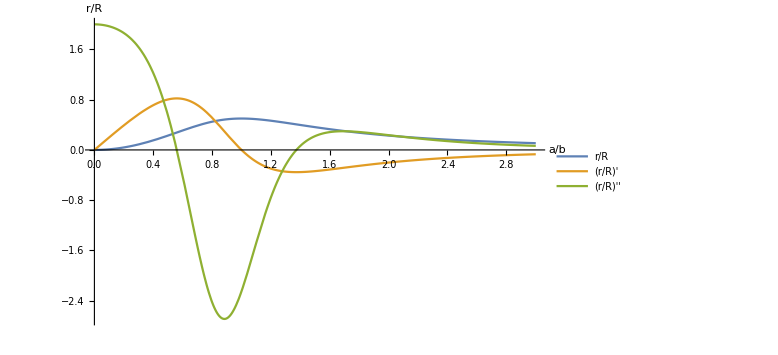

```mathematica
Plot[{getRho[a],rhoD1[a],rhoD2[a]},{a,0,3},PlotLegends->(Style[#,20]&/@{"r/R","(r/R)'","(r/R)''"}),
AxesStyle->20,PlotRange->All,AxesLabel->{"a/b","r/R"},ImageSize->Large]
```

```mathematica
a/.FindRoot[rhoD1[a],{a,1.1}]
```

1.

```mathematica
a/.FindRoot[rhoD2[a],{a,#}]&/@{.5,1.5}
```

{0.559964,1.37285}

```mathematica
FindRoot[rhoD2[a],{a,.5}]
```

{a→0.559964}

```mathematica
rhoSols[1/3.]
```

{-0.629016,0.629016,-1.58978,1.58978}

```mathematica
rhoSols[ρ][[4]]//TeXForm
```

\sqrt{\frac{\rho ^2+2 \sqrt{1-2 \rho } (\rho +1)+2}{\rho  (\rho +4)}}

TODO: Solution : get the axis ratio. get the mittenpunk. draw ellipse with center on mittenpunkt, passing thru all vertices. but how to rotate it? over constrained?

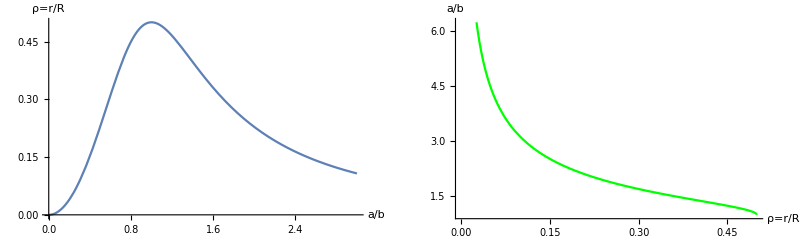

```mathematica
Module[{pA,pR},
pA=Plot[getRho[a],{a,0,3},AxesLabel->{"a/b","ρ=r/R"},AxesStyle->16];
pR=Plot[{rhoSols[ρ][[4]]},{ρ,0,.5},AxesLabel->{"ρ=r/R","a/b"},AxesStyle->16,PlotStyle->{Red,Green}];
GraphicsRow[{pA,pR},ImageSize->800]]
```

### Draw It

```mathematica
Clear@drawCB;
drawCB[a_,{x0_,y0_},theta_,x_,opts:OptionsPattern[]]:=Module[{ellPlot,orbitData,orbit,normals,comb,origin,lgt=.5},
ellPlot=plotEll[a];
orbitData=getOrbitData[N[a],N[x], FilterRules[{opts}, Options[getOrbitData]]];(* N for speed *)
(* half-angle to display α at bisector *)
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
origin=Graphics@{PointSize@Large,Blue,Point@{0,0},Rotate[Text[Style["M",20],{0,0},{-1.5,-1}],-theta],Dashed,Line[{{-a,0},{a,0}}],Line[{{0,-1},{0,1}}]};
comb=Show[{ellPlot,drawOrbit[orbitData,lgt,False,20],origin}];
Show[Graphics@Translate[Rotate[comb[[1]],theta],{x0,y0}],
ImageSize->Medium,
AspectRatio->Automatic,
Axes->True,
PlotRange->{{-2,3},{-1,2}},Frame->True,AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style["a="<>nf@a<>"; x="<>nf@x,20]]];
```

```mathematica
drawCB[1.5,{1,.5},toRad[30.],.3]
```

-Graphics-

-Graphics-

```mathematica
Clear@circumSystem;(*solve for b,t*)
circumSystem[P1_,P2_,A_]:=Module[{ct,st,P1p,P2p,eqn1,eqn2},
st=Sin@t;ct=Cos@t;
P1p=rot[P1,-st,ct];
P2p=rot[P2,-st,ct];
eqn1=P1p[[1]]^2+(A P1p[[2]])^2==(A b)^2;
eqn2=P2p[[1]]^2+(A P2p[[2]])^2==(A b)^2;
(* eqn3=FullSimplify[P2p[[1]]^2+(A P2p[[2]])^2-(A b)^2==0,A>0&&b>0]; *)
{eqn1,eqn2}];circumSystem[{x1,y1},{x2,y2},A](*//FullSimplify[#,A>1&&b∈Reals]&*)
```

{A^2 (y1 Cos[t]-x1 Sin[t])^2+(x1 Cos[t]+y1 Sin[t])^2==A^2 b^2,A^2 (y2 Cos[t]-x2 Sin[t])^2+(x2 Cos[t]+y2 Sin[t])^2==A^2 b^2}

```mathematica
Clear@solveCircum;
solveCircum[orbit_]:=Module[{sides,mit,cos123,rhoCos,A,sols0,sols,ts,bs,as,circSys},
sides=triLengths@orbit;
mit=getMittenTrilin[orbit,RotateLeft@sides];
cos123=getTriCosines[orbit];
rhoCos=Total@cos123-1;(*r/R=cosA+cosB+cosC-1*)
(*Print["rhoCos: " ,rhoCos,", r/R: " ,getInradius[sides]/getCircumradius[sides]];*)
A=rhoSols[rhoCos][[4]];
circSys=circumSystem[orbit[[1]]-mit,orbit[[2]]-mit,A];
sols0=NSolve[circSys,{t,b}]//Quiet;
sols=Select[{t,b}/.sols0,(First[#]∈Reals&&Second[#]∈Reals)&];
ts=(#[[1]]&/@sols);
bs=(#[[2]]&/@sols);
as=A*bs;
(* keep only those sols which pass through P3 *)
Module[{P3ps,P3ok,errors},
P3ps=rot[orbit[[3]]-mit,-Sin@#,Cos@#]&/@ts;
errors=MapThread[ellError[#1,#2,#3]&,{as,bs,P3ps}];
(*Print["errors: ",errors];*)
P3ok=(Abs[#]<10^-6)&/@errors;
sols=Pick[sols,P3ok];
ts=Pick[ts,P3ok];
as=Pick[as,P3ok];
bs=Pick[bs,P3ok];
];
{
"rhoCos"->rhoCos,
"A"->A,
"mit"->mit,
"sols"->sols,
"ts"->ts,
"as"->A*bs,
"bs"->bs
}];
```

```mathematica
tbSols=solveCircum[{{0,0},{1.,0},{.5,Sqrt[3]/1.25}}]
```

{rhoCos→0.448429,A→1.25291,mit→{0.5,0.551208},sols→{{-1.5708,-0.665994},{1.5708,-0.665994},{-1.5708,0.665994},{1.5708,0.665994}},ts→{-1.5708,1.5708,-1.5708,1.5708},as→{-0.834433,-0.834433,0.834433,0.834433},bs→{-0.665994,-0.665994,0.665994,0.665994}}

```mathematica
Clear@transfGr;
transfGr[gr_,scale_,theta_,trans_]:=Graphics@Translate[Rotate[Scale[gr[[1]],scale],theta],trans];
```

```mathematica
Clear@drawSolCB;drawSolCB[tri_,showCtrs_:False]:=Module[{cbs,t,a,b,x0,y0,ell,rotEll,gr,inc,cir,mit,axes,rotAxes},
cbs=solveCircum[tri];
{x0,y0}="mit"/.cbs;
a=First["as"/.cbs];
b=First["bs"/.cbs];
t=First["ts"/.cbs];
ell=plotEll[1];
mit="mit"/.cbs;
rotEll=transfGr[ell,{a,b},t,mit];
(*rotEll=MapThread[transfGr[ell,{#1,#2},#3,mit]&,{"as"/.cbs,"bs"/.cbs,"ts"/.cbs}];*)
axes=Graphics@{Red,Dashed,Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]};
rotAxes=transfGr[axes,{a,b},t,mit];
inc="inc"/.cbs;
cir="cir"/.cbs;
gr=Graphics[{
PointSize@Large,FaceForm@None,
{Red,Point@mit,Text[Style["M",16],mit,{-1.5,-1.5}]},
{Black,Point@tri,EdgeForm@Black,Polygon@tri},
If[showCtrs,{{Darker@Green,Dashed,Circle[inc,"inradius"/.cbs],Point@inc},
{Blue,Dashed,Circle[cir,"circumradius"/.cbs],Point@cir}},{}]
}];
Show[{rotEll,rotAxes,gr},
Axes->True,Frame->True,AspectRatio->Automatic,PlotRange->{{-3,3},{-3,3}}]];
```

```mathematica
drawSolCB[{{.1,.2},{1.1,.3},{1.5,2.3}}]
```

-Graphics-

```mathematica
Manipulate[drawSolCB[{P1,P2,P3}],
{{P1,{2.,0}},Locator},
{{P2,{-1,2}},Locator},
{{P3,{1,-2}},Locator}
]
```

#### Circumbilhar Ronaldo

```mathematica
circRon[a_,b_,x_,y_]=-b^2*(a+Sqrt[a^2+b^2])x^2+b(a^2+a*Sqrt[(a-1)^2+b^2]+a*Sqrt[a^2+b^2]-b^2+Sqrt[(a-1)^2+b^2]Sqrt[a^2+b^2]-a-Sqrt[a^2+b^2])*x*y+(-a^2*Sqrt[(a-1)^2+b^2]+b^2*a-a*Sqrt[(a-1)^2+b^2]*Sqrt[a^2+b^2]-b^2)*y^2+b^2(a+Sqrt[a^2+b^2])*x+b^3*y;
```

```mathematica
Collect[circRon[a,b,x,y],{x,y}]
```

-b^2 (a+√(a^2+b^2)) x^2+b^3 y+(-b^2+a b^2-a^2 √((-1+a)^2+b^2)-a √((-1+a)^2+b^2) √(a^2+b^2)) y^2+x (b^2 (a+√(a^2+b^2))+b (-a+a^2-b^2+a √((-1+a)^2+b^2)-√(a^2+b^2)+a √(a^2+b^2)+√((-1+a)^2+b^2) √(a^2+b^2)) y)